```mathematica
(*
consulta = "df = pd.read_sql(\"\"\"SELECT patient_id,frace,document_id,token_cancer from Alltokens where document_id 
    between 0 and 1000 and token_cancer in ('CANCER_CONCEPT', 'COMORBIDITY', 'AGE', 'TNM', 'TREATMENT_NAME','DRUG','SURGERY')
    group by document_id,patient_id,frace,token_cancer \"\"\" , con)
    print(df.head(10))
    df.to_csv('alltokens.csv', index=False) ";
*)
```

```mathematica
data=Import["C:\\Users\\brian\\Documents\\00-SEMESTRE-2003-II\\Sistemas complejos\\Proyecto\\alltokens.csv", "Data"];
size = Length[data];
Table[data[[i,j]],{i,Length[data]},{j,Length[data[[1]]]}] //TableView;
```

Número de registros considerados:

```mathematica
numRegToEval = 500;
```

ReAjuste de términos sobre dataset para facilitar la visualización del grafo

```mathematica
reglasTokens = {
"AGE"-> "Ag",
"CANCER_CONCEPT" -> "CC",
"COMORBIDITY"-> "Cm",
"DRUG" -> "Dg",
"SURGERY"-> "Sg",
"TNM"-> "TNM",
"TREATMENT_NAME"-> "TN"
};
```

```mathematica
dataFixed = data;
```

```mathematica
dataFixed // TableView;
```

```mathematica
(*Cambio sobre los tokens para su visualizacion*)
dataFixed = dataFixed /. reglasTokens;
(*Cambio registros pacientes - prefijo P*)
Table[dataFixed[[i,1]]= "P:"<>ToString[dataFixed[[i,1]]],{i, 2,numRegToEval}];
(*Cambio registros #doc historia - prefijo H*)
Table[dataFixed[[i,3]]= "H:"<>ToString[dataFixed[[i,3]]],{i, 2,numRegToEval}];
```

```mathematica
EdgeStyling[i_,data_]:= 
Switch[data[[i,4]],
"Ag",Style[data[[i,2]]<-> data[[i,3]],Green],
"CC",Style[data[[i,2]]<-> data[[i,3]],Blue],
"Cm",Style[data[[i,2]]<-> data[[i,3]],Yellow],
"Dg",Style[data[[i,2]]<-> data[[i,3]],Red],
"Sg",Style[data[[i,2]]<-> data[[i,3]],Orange],
"TNM",Style[data[[i,2]]<-> data[[i,3]], Purple],
"TN",Style[data[[i,2]]<-> data[[i,3]], Magenta]];
```

PRUEBA CAMBIO EDGE STYLING  definicion de diccionario con los nodos de cada tipo de token

```mathematica
dicTokens=<|"Ag"->{},"CC"->{},"Cm"->{},"Dg"->{},"Sg"->{},"TNM"->{},"TN"->{}|>;
```

```mathematica
EdgeStyling[i_,data_]:= Module[{},
AppendTo[dicTokens[data[[i,4]]],data[[i,2]]];
Switch[data[[i,4]],
"Ag",Style[data[[i,2]]<-> data[[i,3]],Green],
"CC",Style[data[[i,2]]<-> data[[i,3]],Blue],
"Cm",Style[data[[i,2]]<-> data[[i,3]],Yellow],
"Dg",Style[data[[i,2]]<-> data[[i,3]],Red],
"Sg",Style[data[[i,2]]<-> data[[i,3]],Orange],
"TNM",Style[data[[i,2]]<-> data[[i,3]], Purple],
"TN",Style[data[[i,2]]<-> data[[i,3]], Magenta]]
];
```

```mathematica
nodos = {};
GenerateGraph[data_]:= Module[{doc},
doc = data[[2,3]];
AppendTo[nodos,Labeled[data[[2,1]]<->data[[2,3]],"patient"]];
For[i=2,i<numRegToEval,i++,
AppendTo[nodos,Labeled[EdgeStyling[i,data],data[[i,4]]]];
If[doc != data[[i,3]],AppendTo[nodos,Labeled[data[[i,1]]<->data[[i,3]],"patient"]]; doc=data[[i,3]]];]]

GenerateGraph[dataFixed];
initialGraph = Graph[nodos];
(*SimpleGraph[gp]*)
```

Ajuste de diccionario de nodos en el grafo

```mathematica
dicTokens=AssociationThread[Keys[dicTokens]->Map[DeleteDuplicates,Values[dicTokens]]];
```

Definición del tamaño de los nodos según su grado y arreglo de visualización del grafo

```mathematica
VertexSizes[graph_]:=Module[{sizesVertex={}},
grados=VertexDegree[graph];
vertexs= VertexList[graph];
Table[AppendTo[sizesVertex,If[StringContainsQ[vertexs[[i]],"P:"|"H:"],vertexs[[i]]->1,vertexs[[i]]->1+0.1grados[[i]]]],{i,1,VertexCount[graph]}];
sizesVertex
];
```

```mathematica
shownGraph=Graph[ nodos, VertexLabels->Placed[Automatic,Center], VertexSize->VertexSizes[initialGraph], GraphLayout->"GravityEmbedding"];
```

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[197,P:|H:].

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[67,P:|H:].

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[88,P:|H:].

General::stop: Further output of StringContainsQ::strse will be suppressed during this calculation.

Parte pendiente de revisar ---------

```mathematica
(*Seccion que busca sacar la que sería la lista de nodos particular en una columna, en este caso documentos, con el fin de poderles darles estilo de manera individual*)
documentos = {};
Table[AppendTo[documentos,dataFixed[[i,3]]],{i,2, numRegToEval}];
Table[dataFixed[[i,1]],{i, 2,numRegToEval}];
documentos=DeleteDuplicates[documentos];
```

```mathematica
(*Resaltando nodos de tokens*)
shownGraph=HighlightGraph[shownGraph,Style[dicTokens["Ag"],LightGreen]];
shownGraph =HighlightGraph[shownGraph,Style[dicTokens["CC"],LightBlue]];
shownGraph=HighlightGraph[shownGraph,Style[dicTokens["Cm"],LightYellow]];
shownGraph=HighlightGraph[shownGraph,Style[dicTokens["Dg"],LightRed]];
shownGraph=HighlightGraph[shownGraph,Style[dicTokens["Sg"],LightOrange]];
shownGraph=HighlightGraph[shownGraph,Style[dicTokens["TNM"],LightPurple]];
shownGraph=HighlightGraph[shownGraph,Style[dicTokens["TN"],LightMagenta]];
(*shownGraph = HighlightGraph[shownGraph, documentos, GraphHighlightStyle -> "VertexConcaveDiamond"];*)
```

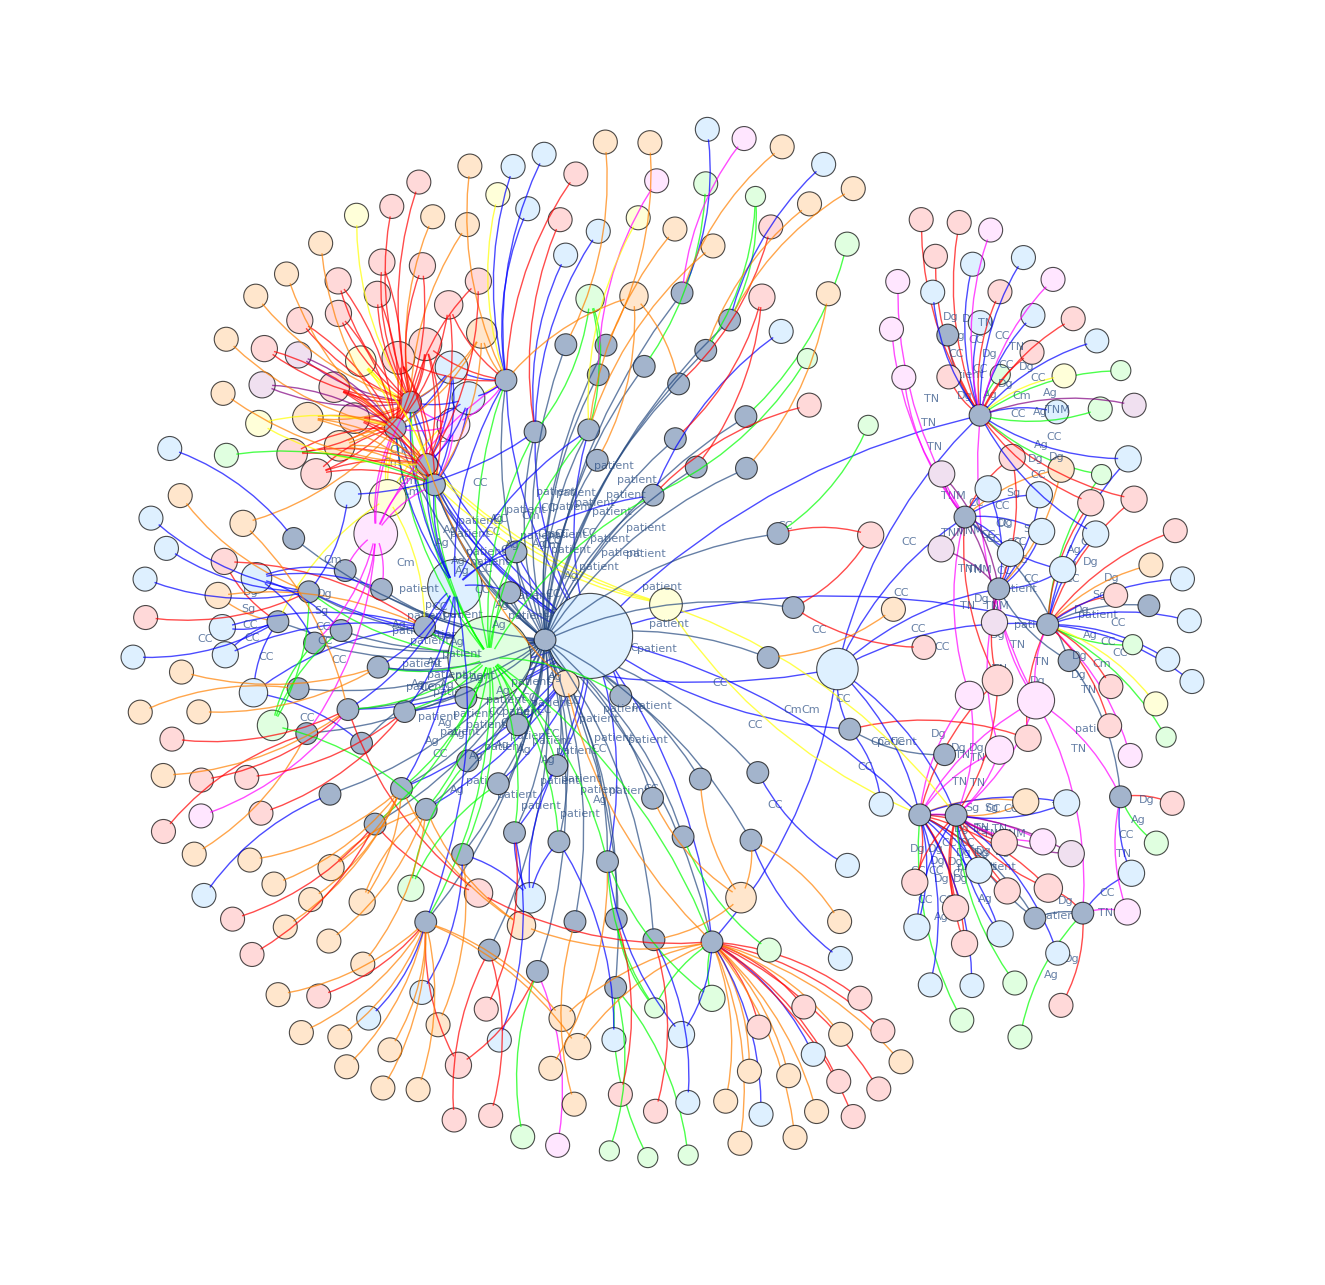

```mathematica
shownGraph
```